```mathematica
Plot3D[Sin[x+ Cos[y^2 ]], {x,-3,3},{y,-3,3}, Mesh->None,ColorFunction->Hue,PlotLegends->Automatic,PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+ Cos[y^2 ]], {x,-3,3},{y,-3,3}, Mesh->Full,ColorFunction->"SolarColors",PlotLegends->Automatic,PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+ Cos[y^2 ]], {x,-3,3},{y,-3,3}, Mesh->6 ,ColorFunction->"Automatic",PlotLegends->Automatic,PlotTheme->"Detailed", MeshShading->{{Yellow, Orange}, {Pink, Red}}]
```

-Graphics3D-

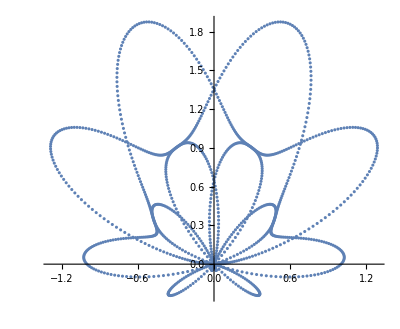

```mathematica
ListPolarPlot[Table[{θ,Sin[θ]+Sin[5θ/2]^3 },{θ,0,4π,0.01}]]
```

```mathematica
Animate[Plot3D[Sin[x+a]Sin[y+b],{x,0,2π},{y,0,2π},PlotRange->1],{a,0,π},{b,0,π},AnimationRunning->False]
```

```mathematica
Animate[Plot3D[Sin[x+a]Sin[y+b],{x,0,2π},{y,0,2π},PlotRange->1],{a,0,π},{b,0,π},AnimationRunning->True]
```

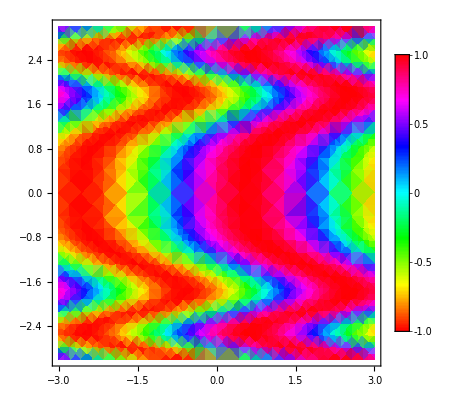

```mathematica
DensityPlot[Sin[x+ Cos[y^2 ]], {x,-3,3},{y,-3,3}, Mesh->None,ColorFunction->Hue,PlotLegends->Automatic,PlotTheme->"Detailed"]
```

```mathematica
ContourPlot3D[(2(4/3 x)^2 + 2y^2 + z^2 -1)^3 -(4/3 x)^2 z^3 /10 -y^2 z^3, {x,-2,2},{y,-2,2},{z,-2,2}, MaxRecursion->6, Mesh->None,Contours->{0}, Boxed->False,PlotRange->All,Axes->False,ViewPoint->{2,0.1,0.5}, ContourStyle->Opacity[0.8]]
```

-Graphics3D-

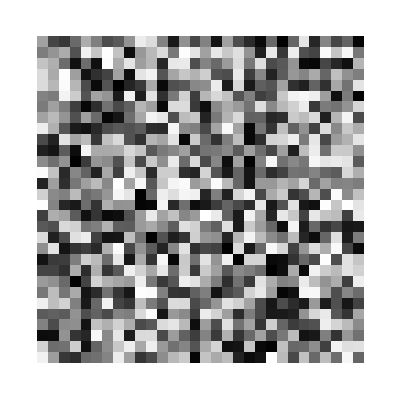

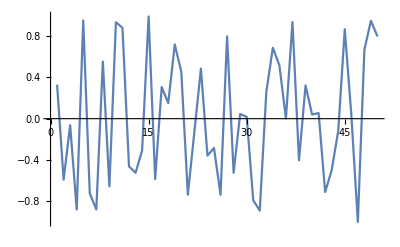

```mathematica
ArrayPlot[RandomReal[{-2,2},{30,30}]]
ListLinePlot[RandomReal[{-1,1},50,WorkingPrecision->7]]
```

```mathematica
(*Define the harmonic motion equation*)eqn=m*x''[t]+k*x[t]==0;

(*Solve the equation using DSolve*)
sol=DSolve[eqn,x[t],t]

(*Extract the solution*)
x[t]=x[t]/.sol[[1]]

(*Display the solution*)
x[t]
```

{{x[t]→C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]}}

C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]

C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]

```mathematica
(*we can use Manipulate command for this*)
Manipulate[Module[{sol,x1,x2},sol=NDSolve[{x1''[t]+k1/m1 x1[t]+k2/m1 (x1[t]-x2[t])==0,x2''[t]+k1/m2 x2[t]+k2/m2 (x2[t]-x1[t])==0,x1[0]==x10,x1'[0]==v10,x2[0]==x20,x2'[0]==v20},{x1,x2},{t,0,tmax}];
Plot[Evaluate[{x1[t],x2[t]}/.sol],{t,0,tmax},PlotRange->{{0,tmax},{-1,1}},PlotStyle->{Blue,Red},AxesLabel->{"Time","Displacement"},PlotLegends->{"Mass 1","Mass 2"}]],{{k1,1},0.1,10,Appearance->"Labeled"},{{k2,1},0.1,10,Appearance->"Labeled"},{{m1,1},0.1,10,Appearance->"Labeled"},{{m2,1},0.1,10,Appearance->"Labeled"},{{x10,1},-1,1,Appearance->"Labeled"},{{x20,1},-1,1,Appearance->"Labeled"},{{v10,0},-1,1,Appearance->"Labeled"},{{v20,0},-1,1,Appearance->"Labeled"},{{tmax,10},1,20,Appearance->"Labeled"}]
```

```mathematica
ColorConvert[RGBColor[0.25098,0.501961,0.501961],"Grayscale"]
```

GrayLevel[0.42691768099999994]

```mathematica
Manipulate[Plot3D[Sin[√(x^2 + y^2)],{x,-5,5},{y,-5,5},PlotRange->{-1,1},MeshFunctions->{#1 & , #2 & },MeshStyle->{Red, Blue},ColorFunction->"Rainbow",PlotStyle->Opacity[opacity],PerformanceGoal->"Quality",BoxRatios->{1,1,1},PlotLabel->StringForm["a = `1`, b = `2`",a,b]],{{a,1,"a"},0.1,5,0.1},{{b,1,"b"},0.1,5,0.1},{{opacity,0.7,"Opacity"},0,1}]
```

```mathematica
Animate[Plot3D[Sin[√(x^2 + y^2)],{x,-5,5},{y,-5,5},PlotRange->{-1,1},MeshFunctions->{#1 & , #2 & },MeshStyle->{Red, Blue},ColorFunction->"Rainbow",PlotStyle->Opacity[opacity],PerformanceGoal->"Quality",BoxRatios->{1,1,1},PlotLabel->StringForm["a = `1`, b = `2`",a,b]],{{a,1,"a"},0.1,5,0.1},{{b,1,"b"},0.1,5,0.1},{{opacity,0.7,"Opacity"},0,1}]
```

```mathematica
Manipulate[Plot3D[Sin[√(x^2 + y^2)],{x,-5,5},{y,-5,5},PlotRange->{-1,1},MeshFunctions->{#1 & , #2 & },MeshStyle->{Red, Blue},ColorFunction->"SolarColors",PlotStyle->Gray,BoxRatios->{1,1,1},PlotLabel->StringForm["a = `1`, b = `2`",a,b]],{{a,1,"a"},0.1,5,0.1},{{b,1,"b"},0.1,5,0.1}]
```

```mathematica
Y[l_,m_,theta_,phi_]:=Re[SphericalHarmonicY[l,m,theta,phi]]*Re[SphericalHarmonicY[l,m,theta,phi]]

Row[{SphericalPlot3D[Y[1,-1,theta,phi],{theta,0,Pi},{phi,0,2*Pi},PlotRange->All,AxesLabel->{Style["x",Medium],Style["y",Medium],Style["z",Medium]},ImageSize->Medium],SphericalPlot3D[Y[1,1,theta,phi],{theta,0,Pi},{phi,0,2*Pi},PlotRange->All,AxesLabel->{Style["x",Medium],Style["y",Medium],Style["z",Medium]},ImageSize->Medium]}]
```

-Graphics3D--Graphics3D-

```mathematica
fpx[theta_,phi_]:=(Sqrt[3]*Sin[theta]/2*Cos[phi]/Sqrt[Pi])^2;
fpy[theta_,phi_]:=(Sqrt[3]*Sin[theta]/2*Sin[phi]/Sqrt[Pi])^2;

Row[{SphericalPlot3D[fpx[theta,phi],{theta,0,Pi},{phi,0,2*Pi},PlotRange->All,AxesLabel->{Style["x",Medium],Style["y",Medium],Style["z",Medium]},ImageSize->Medium],SphericalPlot3D[fpy[theta,phi],{theta,0,Pi},{phi,0,2*Pi},PlotRange->All,AxesLabel->{Style["x",Medium],Style["y",Medium],Style["z",Medium]},ImageSize->Medium]}]
```

-Graphics3D--Graphics3D-

```mathematica
px[θ_,φ_]=SphericalHarmonicY[1,-1,θ,φ]-SphericalHarmonicY[1,1,θ,φ]//FullSimplify;

py[θ_,φ_]=SphericalHarmonicY[1,-1,θ,φ]+SphericalHarmonicY[1,1,θ,φ]//FullSimplify;

pz[θ_,φ_]=SphericalHarmonicY[1,0,θ,φ]//FullSimplify;

SphericalPlot3D[Abs[px[θ,φ]]^2,{θ,0,π},{φ,0,2 π},PlotRange->All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[py[θ,φ]]^2,{θ,0,π},{φ,0,2 π},PlotRange->All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Abs[pz[θ,φ]]^2,{θ,0,π},{φ,0,2 π},PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[ParametricPlot[{Sin[θ],Cos[θ]}LegendreP[n,Cos[θ]],{θ,0,If[OddQ[n],1,2]Pi},PlotStyle->Directive[{FaceForm[RGBColor[0.682353,0.866667,0.862745]],EdgeForm[Black]}],AxesOrigin->{0,0},Axes->If[ticks===Automatic,{True,True},{False,False}],Ticks->ticks,PlotRange->1.1,ImageSize->{500,500},PlotLabel->Style[With[{n=n},HoldForm[r==LegendreP[n,Cos[θ]]]],14]]/.Line->Polygon,{{n,0,"order"},0,10,1,Appearance->"Labeled"}, {{ticks,None,"show scale"},{None,Automatic},ControlType->Checkbox}]
```